```mathematica
magic[primeList_] :=N[(∏_p^primeList (1/p+1)^(1/(log(p))))/(2^(∑_p^primeList 1/(log(p))))]
```

```mathematica
Sort[
Select[
Table[{sample, magic[sample], magic[sample] - 1/E}, 
{sample, Subsets[Table[Prime[n],{n,2,25}],{4}]}
],
Abs[#[[3]] ] ≤0.0005 &
],
#1[[3]] < #2[[3]] &
]
```

{{{5,13,17,19},0.367437,-0.000442675},{{3,7,31,89},0.367441,-0.000438599},{{3,11,19,67},0.367451,-0.000428117},{{5,7,19,43},0.367459,-0.000420797},{{3,7,47,53},0.367477,-0.000402395},{{3,13,17,59},0.367599,-0.000280107},{{3,7,43,59},0.367621,-0.000258219},{{3,5,73,79},0.367657,-0.000222328},{{3,7,37,71},0.367675,-0.000204618},{{5,7,13,83},0.367704,-0.000175266},{{3,11,17,83},0.367704,-0.000175127},{{3,5,61,97},0.367733,-0.000145951},{{3,5,71,83},0.3679,0.0000210465},{{3,5,67,89},0.367981,0.00010123},{{7,11,13,19},0.367991,0.000111119},{{3,7,37,73},0.368022,0.000142224},{{3,13,17,61},0.368045,0.000165741},{{3,7,43,61},0.368067,0.000187655},{{5,7,17,53},0.368126,0.000246197},{{3,11,23,53},0.368168,0.000288834},{{3,11,19,71},0.368187,0.000307585},{{3,11,31,37},0.368238,0.000358697},{{3,5,73,83},0.368248,0.000368101},{{3,13,29,31},0.368322,0.000442297}}

```mathematica
Prime[25]
```

97

```mathematica
Subsets[Table[Prime[n],{n,2,10}],{4}]
```

{{3,5,7,11},{3,5,7,13},{3,5,7,17},{3,5,7,19},{3,5,7,23},{3,5,7,29},{3,5,11,13},{3,5,11,17},{3,5,11,19},{3,5,11,23},{3,5,11,29},{3,5,13,17},{3,5,13,19},{3,5,13,23},{3,5,13,29},{3,5,17,19},{3,5,17,23},{3,5,17,29},{3,5,19,23},{3,5,19,29},{3,5,23,29},{3,7,11,13},{3,7,11,17},{3,7,11,19},{3,7,11,23},{3,7,11,29},{3,7,13,17},{3,7,13,19},{3,7,13,23},{3,7,13,29},{3,7,17,19},{3,7,17,23},{3,7,17,29},{3,7,19,23},{3,7,19,29},{3,7,23,29},{3,11,13,17},{3,11,13,19},{3,11,13,23},{3,11,13,29},{3,11,17,19},{3,11,17,23},{3,11,17,29},{3,11,19,23},{3,11,19,29},{3,11,23,29},{3,13,17,19},{3,13,17,23},{3,13,17,29},{3,13,19,23},{3,13,19,29},{3,13,23,29},{3,17,19,23},{3,17,19,29},{3,17,23,29},{3,19,23,29},{5,7,11,13},{5,7,11,17},{5,7,11,19},{5,7,11,23},{5,7,11,29},{5,7,13,17},{5,7,13,19},{5,7,13,23},{5,7,13,29},{5,7,17,19},{5,7,17,23},{5,7,17,29},{5,7,19,23},{5,7,19,29},{5,7,23,29},{5,11,13,17},{5,11,13,19},{5,11,13,23},{5,11,13,29},{5,11,17,19},{5,11,17,23},{5,11,17,29},{5,11,19,23},{5,11,19,29},{5,11,23,29},{5,13,17,19},{5,13,17,23},{5,13,17,29},{5,13,19,23},{5,13,19,29},{5,13,23,29},{5,17,19,23},{5,17,19,29},{5,17,23,29},{5,19,23,29},{7,11,13,17},{7,11,13,19},{7,11,13,23},{7,11,13,29},{7,11,17,19},{7,11,17,23},{7,11,17,29},{7,11,19,23},{7,11,19,29},{7,11,23,29},{7,13,17,19},{7,13,17,23},{7,13,17,29},{7,13,19,23},{7,13,19,29},{7,13,23,29},{7,17,19,23},{7,17,19,29},{7,17,23,29},{7,19,23,29},{11,13,17,19},{11,13,17,23},{11,13,17,29},{11,13,19,23},{11,13,19,29},{11,13,23,29},{11,17,19,23},{11,17,19,29},{11,17,23,29},{11,19,23,29},{13,17,19,23},{13,17,19,29},{13,17,23,29},{13,19,23,29},{17,19,23,29}}

```mathematica
(∏_p^primeList (1/p+1)^(1/(log(p))))/(2^(∑_p^primeList 1/(log(p))))<1/ⅇ
```

```mathematica
(∏_p^primeList (1/p+1)^(1/(log(p))))/(2^(∑_p^primeList 1/(log(p))))>1/ⅇ
```

```mathematica
Timing[
Sort[
Select[
Table[{sample, magic[sample], magic[sample] - 1/E}, 
{sample, Subsets[Table[Prime[n],{n,2,25}],{5}]}
],
Abs[#[[3]] ] ≤0.0005 &
],
#1[[3]] < #2[[3]] &
]
]
```

{628.778,{{{13,19,23,53,61},0.36738,-0.00049938},{{5,23,59,67,97},0.36738,-0.000498992},{{11,17,23,61,89},0.367388,-0.000491401},{{5,43,47,53,67},0.367388,-0.000491268},{{11,17,37,43,67},0.36739,-0.000489545},{{11,17,19,83,89},0.367391,-0.000488165},{{7,31,37,43,73},0.367393,-0.00048654},{{5,41,47,53,71},0.367393,-0.00048636},{{11,17,37,41,71},0.367395,-0.000484637},{{11,19,23,61,73},0.367402,-0.000477914},{{3,59,67,79,97},0.367402,-0.000477449},{{5,23,67,71,79},0.367403,-0.000476393},{{11,17,29,53,73},0.367404,-0.000475396},{{5,37,41,53,97},0.367408,-0.00047096},{{7,13,61,79,89},0.367409,-0.000469996},{{7,23,37,59,79},0.36741,-0.000469124},{{13,17,31,43,61},0.367416,-0.000463063},{{5,29,43,79,83},0.367417,-0.000462125},{{5,19,61,89,97},0.36742,-0.000459013},{{7,13,61,73,97},0.367421,-0.000458938},{{7,23,41,61,67},0.367429,-0.000450458},{{7,19,41,67,83},0.367432,-0.000447222},{{5,29,47,71,83},0.367433,-0.000446559},{{7,23,29,73,89},0.367448,-0.000431473},{{5,29,37,83,97},0.367448,-0.000431157},{{13,19,31,37,61},0.36745,-0.000429667},{{7,29,31,59,71},0.367451,-0.000428397},{{11,13,29,71,89},0.367452,-0.000427756},{{7,23,31,71,83},0.367453,-0.000426218},{{5,31,47,61,89},0.367456,-0.000423409},{{13,19,29,41,59},0.367458,-0.000421403},{{13,19,23,41,83},0.36746,-0.000419224},{{3,61,67,83,89},0.36746,-0.000419212},{{13,17,29,43,67},0.367473,-0.000406137},{{13,17,29,41,71},0.367478,-0.000401228},{{11,19,29,53,61},0.367483,-0.000396642},{{5,23,59,73,89},0.367485,-0.000394348},{{11,17,31,53,67},0.367489,-0.000390065},{{5,17,79,83,97},0.367492,-0.000387086},{{11,17,37,47,61},0.367494,-0.00038548},{{7,29,41,43,71},0.3675,-0.000379348},{{5,29,41,79,89},0.367502,-0.000377137},{{11,13,43,47,83},0.367506,-0.000373222},{{3,59,73,79,89},0.367507,-0.000372799},{{13,19,29,37,67},0.367507,-0.000372736},{{5,29,47,67,89},0.367513,-0.000366477},{{5,29,41,73,97},0.367513,-0.000366076},{{17,19,29,37,43},0.367514,-0.000365276},{{7,17,59,61,73},0.367522,-0.00035793},{{17,19,23,31,73},0.367532,-0.000347063},{{7,23,31,67,89},0.367533,-0.000346132},{{5,37,41,61,83},0.367534,-0.000345485},{{5,41,43,59,71},0.367537,-0.000342217},{{11,23,31,43,53},0.367539,-0.00034018},{{7,11,71,89,97},0.367549,-0.000330827},{{13,17,19,67,79},0.367551,-0.000328657},{{7,13,59,83,89},0.367554,-0.000325756},{{7,29,37,47,73},0.367554,-0.000325535},{{7,19,41,59,97},0.367555,-0.000324472},{{11,19,31,43,71},0.367558,-0.000321462},{{7,23,41,53,79},0.367559,-0.000320581},{{11,23,29,41,61},0.36756,-0.000319701},{{11,13,31,73,79},0.36756,-0.000319176},{{11,19,29,41,83},0.367563,-0.000316464},{{5,29,53,59,89},0.367566,-0.000313057},{{5,23,53,83,89},0.367569,-0.000310878},{{7,23,47,53,67},0.36757,-0.000309919},{{7,17,43,67,97},0.36757,-0.000309202},{{7,19,43,67,79},0.367573,-0.000306772},{{7,17,41,71,97},0.367575,-0.000304291},{{13,17,29,47,61},0.367577,-0.000302048},{{7,19,41,71,79},0.367578,-0.000301861},{{3,59,61,89,97},0.367583,-0.000296452},{{5,23,61,71,89},0.367584,-0.000295396},{{5,37,43,67,71},0.367586,-0.000293539},{{5,19,71,83,89},0.367587,-0.000292158},{{7,13,71,73,83},0.367587,-0.000292083},{{7,19,47,67,71},0.367588,-0.000291199},{{3,53,79,83,89},0.36759,-0.000289323},{{7,31,41,47,59},0.367591,-0.000288855},{{5,37,47,59,73},0.367591,-0.0002884},{{11,13,41,47,89},0.367591,-0.000288213},{{7,17,47,73,79},0.367598,-0.000281451},{{13,17,23,43,97},0.367598,-0.000281193},{{7,23,29,79,83},0.367599,-0.000280762},{{5,31,41,67,97},0.367599,-0.00028072},{{7,29,43,47,61},0.367599,-0.000280162},{{5,29,53,71,73},0.3676,-0.000279383},{{13,19,23,43,79},0.367601,-0.000278763},{{3,53,73,83,97},0.367601,-0.00027826},{{7,19,37,67,97},0.367604,-0.000275791},{{7,17,53,61,83},0.367605,-0.000274451},{{3,61,71,79,89},0.367606,-0.00027384},{{17,19,29,31,53},0.367614,-0.000265762},{{13,19,23,47,71},0.367616,-0.000263189},{{3,61,71,73,97},0.367617,-0.000262776},{{5,31,43,73,83},0.367618,-0.000261048},{{7,31,37,41,79},0.367629,-0.000250834},{{13,19,23,37,97},0.367632,-0.00024778},{{5,23,59,79,83},0.367636,-0.000243621},{{5,43,47,59,61},0.367636,-0.000243022},{{11,13,31,61,97},0.367637,-0.000242818},{{5,23,47,89,97},0.367638,-0.000241519},{{5,31,37,83,89},0.367638,-0.000241129},{{7,31,37,47,67},0.367639,-0.00024017},{{7,19,53,59,71},0.367642,-0.000237768},{{3,47,79,89,97},0.367659,-0.000219961},{{11,23,29,31,89},0.367664,-0.000215337},{{13,23,31,37,47},0.367667,-0.000212156},{{7,13,67,73,89},0.367667,-0.000211967},{{11,13,43,53,73},0.367673,-0.000206013},{{7,17,47,61,97},0.367674,-0.000205085},{{5,37,43,61,79},0.367674,-0.000204996},{{5,37,47,53,83},0.367675,-0.000204905},{{7,17,43,73,89},0.367675,-0.000204504},{{7,19,47,61,79},0.367677,-0.000202655},{{5,31,53,67,71},0.367685,-0.000194006},{{5,37,47,61,71},0.36769,-0.000189418},{{17,23,29,31,41},0.367691,-0.000188794},{{13,17,23,59,67},0.367692,-0.0001876},{{7,31,37,53,59},0.367693,-0.000186732},{{11,13,37,53,89},0.367693,-0.00018609},{{11,13,29,67,97},0.367694,-0.000185858},{{11,23,29,47,53},0.3677,-0.000179111},{{11,17,29,43,97},0.367701,-0.000178394},{{5,31,41,73,89},0.367703,-0.000176014},{{11,19,29,43,79},0.367703,-0.000175963},{{7,19,37,73,89},0.367708,-0.000171084},{{7,23,43,59,67},0.367714,-0.000165707},{{7,23,41,59,71},0.367719,-0.000160794},{{11,19,29,47,71},0.367719,-0.000160385},{{13,17,37,41,53},0.36772,-0.000159545},{{13,17,19,61,89},0.367732,-0.000147587},{{17,19,23,37,59},0.367733,-0.000146714},{{11,19,29,37,97},0.367734,-0.000144972},{{11,17,31,59,61},0.367738,-0.000141751},{{5,41,47,53,73},0.36774,-0.000139783},{{11,17,37,41,73},0.367741,-0.000138059},{{7,37,41,43,53},0.367742,-0.00013765},{{5,23,67,73,79},0.36775,-0.000129807},{{3,59,71,83,89},0.36775,-0.000129524},{{7,19,43,61,89},0.367754,-0.000125691},{{13,17,29,37,83},0.36776,-0.000119708},{{11,13,37,59,79},0.367761,-0.000118811},{{7,23,37,67,71},0.367767,-0.000112092},{{11,29,31,37,47},0.36777,-0.000109337},{{5,31,53,61,79},0.367774,-0.000105439},{{11,17,19,79,97},0.367779,-0.000100866},{{11,13,41,61,67},0.367779,-0.000100128},{{5,29,47,73,83},0.367779,-0.0000999447},{{7,29,37,43,83},0.367782,-0.0000978108},{{11,17,41,43,61},0.367787,-0.0000926626},{{11,17,29,59,67},0.367795,-0.0000847749},{{11,17,23,67,83},0.367797,-0.0000825939},{{7,29,31,59,73},0.367798,-0.0000817663},{{11,13,29,73,89},0.367798,-0.0000811248},{{7,23,31,73,83},0.3678,-0.0000795854},{{11,13,31,71,83},0.367804,-0.000075865},{{11,17,31,47,79},0.367814,-0.0000652269},{{7,23,47,59,61},0.367818,-0.0000615499},{{7,13,67,79,83},0.367818,-0.0000611654},{{5,37,43,59,83},0.367819,-0.0000606521},{{11,19,37,41,61},0.36782,-0.0000592323},{{7,19,47,59,83},0.367821,-0.0000583102},{{13,17,29,41,73},0.367825,-0.0000545715},{{7,17,43,79,83},0.367826,-0.0000536991},{{5,23,61,67,97},0.367826,-0.0000534099},{{5,19,67,83,97},0.367829,-0.0000501701},{{5,29,53,67,79},0.367831,-0.0000484574},{{7,17,47,71,83},0.367841,-0.0000381153},{{11,23,29,43,59},0.367845,-0.0000348482},{{7,29,41,43,73},0.367847,-0.0000326703},{{3,61,67,79,97},0.367848,-0.0000318405},{{5,31,41,79,83},0.367854,-0.0000251971},{{11,19,23,53,89},0.367855,-0.0000245981},{{7,23,37,61,79},0.367856,-0.0000235053},{{7,17,37,83,97},0.367857,-0.000022697},{{7,19,37,79,83},0.367859,-0.0000202653},{{3,67,71,73,89},0.367864,-0.0000156739},{{5,31,47,67,83},0.367865,-0.0000145266},{{7,29,37,41,89},0.367867,-0.0000127383},{{7,13,53,89,97},0.367874,-5.59804×10^-6},{{7,29,31,53,83},0.367881,1.77524×10^-6},{{17,19,23,41,53},0.367881,1.95934×10^-6},{{13,19,31,43,53},0.367883,3.77502×10^-6},{{11,13,31,67,89},0.367884,4.29773×10^-6},{{5,41,43,59,73},0.367884,4.49506×10^-6},{{11,17,31,43,89},0.367891,0.0000117654},{{7,11,73,89,97},0.367895,0.0000158965},{{7,29,31,61,71},0.367897,0.0000172705},{{5,29,43,71,97},0.367897,0.0000177779},{{11,23,29,37,71},0.367898,0.0000187854},{{13,19,29,41,61},0.367904,0.0000242732},{{5,37,41,59,89},0.367904,0.000024429},{{11,19,31,43,73},0.367905,0.0000252701},{{11,13,41,53,79},0.367909,0.0000298736},{{13,17,31,41,67},0.36791,0.0000308572},{{7,17,41,79,89},0.367911,0.0000313836},{{5,31,53,59,83},0.367918,0.000038944},{{11,17,23,59,97},0.36792,0.0000402785},{{11,13,47,53,67},0.36792,0.0000405457},{{17,19,23,29,83},0.367921,0.0000418133},{{7,17,47,67,89},0.367921,0.0000420557},{{7,17,41,73,97},0.367922,0.0000424568},{{11,19,23,59,79},0.367922,0.0000427106},{{7,19,41,73,79},0.367924,0.000044889},{{11,19,31,37,89},0.367925,0.0000452051},{{11,17,43,47,53},0.367927,0.000048014},{{5,23,61,73,89},0.367931,0.0000513609},{{7,31,41,43,67},0.367932,0.0000527635},{{5,37,43,67,73},0.367933,0.000053219},{{5,31,59,61,71},0.367934,0.0000544408},{{5,19,73,83,89},0.367934,0.0000546016},{{7,19,47,67,73},0.367935,0.0000555615},{{5,37,41,71,73},0.367938,0.0000581344},{{7,13,59,79,97},0.367941,0.0000617141},{{11,17,23,71,79},0.367942,0.0000629111},{{11,13,29,79,83},0.367949,0.0000697306},{{13,17,23,47,89},0.36795,0.000070091},{{7,29,31,47,97},0.367951,0.0000711928},{{17,19,31,37,41},0.367951,0.0000717676},{{3,61,73,79,89},0.367952,0.0000729364},{{5,23,53,79,97},0.367956,0.0000766083},{{13,23,31,41,43},0.36796,0.0000807996},{{11,19,37,47,53},0.367961,0.0000814571},{{13,19,23,47,73},0.367963,0.0000835978},{{5,41,43,53,83},0.367967,0.0000880562},{{7,23,43,47,89},0.367971,0.0000919996},{{5,19,71,79,97},0.367975,0.0000953478},{{7,17,53,59,89},0.367975,0.0000955345},{{5,41,43,61,71},0.367983,0.000103555},{{5,31,47,59,97},0.367988,0.000108369},{{7,19,53,59,73},0.367988,0.000109042},{{5,29,59,67,71},0.367991,0.000111447},{{3,59,67,83,97},0.367992,0.000112571},{{5,23,67,71,83},0.367993,0.000113629},{{7,13,61,83,89},0.367999,0.000120036},{{7,23,37,59,83},0.368,0.00012091},{{7,19,41,61,97},0.368001,0.000121322},{{13,19,29,31,89},0.368008,0.000128734},{{7,17,53,71,73},0.368009,0.000129246},{{5,31,47,71,79},0.36801,0.000131005},{{5,29,53,61,89},0.368012,0.000132751},{{3,67,71,79,83},0.368015,0.000135208},{{5,31,37,79,97},0.368026,0.000146431},{{5,31,53,67,73},0.368032,0.000152846},{{7,31,41,47,61},0.368036,0.000156982},{{5,37,47,61,73},0.368037,0.000157438},{{5,41,43,47,97},0.368037,0.00015749},{{11,23,37,41,47},0.368038,0.000158498},{{13,19,29,47,53},0.368044,0.000164995},{{7,11,79,83,97},0.368046,0.000166792},{{11,17,29,47,89},0.368052,0.000172988},{{11,29,31,41,43},0.368063,0.0001837},{{11,13,43,59,67},0.368064,0.000184895},{{7,23,41,59,73},0.368066,0.000186089},{{11,19,29,47,73},0.368066,0.000186499},{{11,13,41,59,71},0.368069,0.000189812},{{3,53,71,89,97},0.36807,0.000190805},{{7,23,29,71,97},0.368079,0.000199378},{{5,29,59,61,79},0.36808,0.000200088},{{5,23,61,79,83},0.368082,0.000202271},{{5,31,43,71,89},0.368087,0.000208039},{{7,19,53,61,71},0.368088,0.000208131},{{5,29,41,83,89},0.368092,0.000213044},{{7,29,41,47,67},0.368093,0.000214005},{{3,59,73,83,89},0.368097,0.000217389},{{7,19,31,89,97},0.368105,0.000225811},{{11,19,37,43,59},0.368105,0.000225822},{{7,23,37,67,73},0.368114,0.000234837},{{5,23,59,71,97},0.368116,0.000236567},{{11,13,37,67,71},0.368118,0.00023856},{{13,23,29,41,47},0.368121,0.000242053},{{5,43,47,53,71},0.368124,0.000244307},{{11,17,37,43,71},0.368125,0.000246033},{{5,41,47,59,67},0.368131,0.000251195},{{3,59,71,79,97},0.368138,0.000258153},{{13,17,23,61,67},0.368138,0.00025836},{{11,17,31,41,97},0.368138,0.000258871},{{7,31,37,53,61},0.368139,0.000259229},{{5,37,43,53,97},0.368139,0.000259737},{{11,19,31,41,79},0.368141,0.000261305},{{13,17,19,67,83},0.368141,0.000261602},{{7,19,47,53,97},0.368142,0.000262081},{{7,29,41,53,59},0.368147,0.000267508},{{7,23,41,53,83},0.368149,0.000269691},{{11,13,31,73,83},0.368151,0.000271099},{{11,19,31,47,67},0.368151,0.000271984},{{7,23,43,61,67},0.36816,0.000280279},{{7,19,43,67,83},0.368163,0.000283522},{{7,23,41,61,71},0.368165,0.000285198},{{7,19,41,71,83},0.368168,0.000288441},{{11,13,47,59,61},0.368169,0.000289151},{{5,37,41,67,79},0.368169,0.000289272},{{17,19,23,37,61},0.368179,0.000299295},{{7,17,47,73,83},0.368188,0.000308884},{{13,19,29,43,59},0.368189,0.000309393},{{13,19,23,43,83},0.368191,0.000311576},{{7,29,37,53,67},0.368196,0.000316267},{{3,61,71,83,89},0.368196,0.000316507},{{11,19,31,53,59},0.368205,0.000325496},{{11,13,37,61,79},0.368207,0.000327232},{{13,17,29,43,71},0.368209,0.000329608},{{7,23,41,47,97},0.368219,0.000339159},{{7,31,37,41,83},0.368219,0.00033955},{{13,23,29,37,53},0.368224,0.000344323},{{11,17,31,53,71},0.368225,0.000345712},{{5,37,53,59,67},0.368233,0.000353468},{{5,29,43,79,89},0.368233,0.000353747},{{7,17,53,67,79},0.36824,0.000360428},{{11,17,29,61,67},0.368241,0.00036131},{{13,19,29,37,71},0.368243,0.000363076},{{7,29,31,61,73},0.368244,0.000364322},{{5,29,43,73,97},0.368244,0.00036483},{{11,23,29,37,73},0.368245,0.000365838},{{7,19,41,67,89},0.368248,0.000368683},{{5,29,47,71,89},0.368249,0.000369348},{{3,47,83,89,97},0.36825,0.000370473},{{11,19,41,43,53},0.368254,0.000374646},{{13,17,19,59,97},0.368264,0.00038459},{{5,29,37,89,97},0.368264,0.000384783},{{5,37,43,61,83},0.368265,0.000385462},{{7,19,47,61,83},0.368267,0.000387806},{{13,17,23,53,79},0.368268,0.000388488},{{7,23,31,71,89},0.368269,0.000389733},{{13,19,23,41,89},0.368276,0.000396743},{{11,19,23,67,71},0.36828,0.000400239},{{5,31,59,61,73},0.368281,0.000401527},{{11,23,31,41,59},0.368282,0.000402588},{{7,19,43,59,97},0.368286,0.000406517},{{13,17,19,71,79},0.368287,0.000407243},{{11,17,23,73,79},0.368289,0.000410006},{{7,23,43,53,79},0.36829,0.000410416},{{11,23,29,43,61},0.368291,0.000411297},{{11,19,29,43,83},0.368294,0.000414541},{{7,13,67,71,97},0.368299,0.000419261},{{13,17,31,47,59},0.3683,0.000420275},{{7,23,47,53,71},0.368305,0.000426019},{{7,17,43,71,97},0.368306,0.000426737},{{5,17,79,89,97},0.368308,0.000428953},{{7,19,43,71,79},0.368309,0.000429172},{{7,23,37,53,97},0.368321,0.000441457},{{7,31,43,47,59},0.368322,0.000442205},{{5,19,73,79,97},0.368322,0.000442473},{{11,13,43,47,89},0.368322,0.000442847},{{5,31,43,67,97},0.36833,0.000450356},{{5,41,43,61,73},0.36833,0.000450688},{{11,23,31,37,67},0.368331,0.000451365},{{5,31,41,71,97},0.368335,0.000455277},{{13,17,31,37,79},0.368338,0.00045837},{{5,29,59,67,73},0.368338,0.000458587},{{7,19,37,71,97},0.36834,0.000460215},{{5,23,67,73,83},0.36834,0.000460771},{{13,17,41,43,47},0.368349,0.000469438},{{5,37,41,61,89},0.36835,0.000470646},{{11,13,37,59,83},0.368351,0.000471785},{{5,31,47,73,79},0.368358,0.000478164},{{7,31,37,43,79},0.36836,0.000480301},{{3,67,73,79,83},0.368362,0.000482371},{{5,31,53,61,83},0.368365,0.000485179},{{11,17,23,61,97},0.368366,0.000486515},{{11,19,23,61,79},0.368368,0.00048895},{{11,17,19,83,97},0.368369,0.000489759},{{11,17,29,53,79},0.368371,0.000491474},{{7,31,37,47,71},0.368375,0.000495908},{{11,19,29,41,89},0.368379,0.000499732}}}

```mathematica
Length[Subsets[Table[Prime[n],{n,2,25}],{5}]]
```

42504

```mathematica
magic[{7,11,13,19}]-1/E
```

```mathematica
0.000111118791846887-0.0003075845061262239
```

-0.000196466

```mathematica
Timing[
Sort[
Select[
Table[{sample, magic[sample], magic[sample] - 1/E}, 
{sample, Subsets[Table[Prime[n],{n,10,25}],{6}]}
],
Abs[#[[3]] ] ≤0.0005 &
],
#1[[3]] < #2[[3]] &
]
]
```

{148.123,{{{37,47,53,61,79,89},0.36738,-0.000499611},{{29,47,61,67,79,97},0.36738,-0.000499378},{{29,43,67,73,79,89},0.367381,-0.000498797},{{37,41,59,61,83,89},0.367384,-0.000495905},{{29,41,71,73,79,89},0.367386,-0.000493889},{{31,43,67,71,79,83},0.367386,-0.000493543},{{37,47,53,61,73,97},0.367391,-0.000488553},{{31,47,59,73,79,83},0.367391,-0.000488407},{{29,47,67,71,73,89},0.367396,-0.000483232},{{29,37,67,73,89,97},0.367412,-0.000467833},{{37,43,61,67,73,83},0.367412,-0.000467156},{{31,37,67,71,83,97},0.367417,-0.000462578},{{37,41,61,71,73,83},0.367417,-0.000462247},{{41,53,59,61,67,71},0.367431,-0.000448815},{{29,53,59,61,79,97},0.367433,-0.000445978},{{37,43,59,67,71,89},0.367435,-0.000443981},{{41,43,47,73,79,83},0.36744,-0.000439365},{{31,43,53,71,89,97},0.367441,-0.000438041},{{29,41,53,83,89,97},0.367446,-0.000433045},{{31,41,59,67,89,97},0.367448,-0.000431166},{{29,53,59,71,73,89},0.36745,-0.00042983},{{29,43,61,67,89,97},0.367457,-0.000422477},{{37,41,47,79,83,89},0.36746,-0.000419455},{{29,41,61,71,89,97},0.367462,-0.000417568},{{31,47,59,61,83,97},0.367467,-0.000412084},{{31,43,59,73,83,89},0.367468,-0.000411503},{{29,59,61,67,71,83},0.36747,-0.00040901},{{31,41,67,71,79,89},0.367471,-0.000408563},{{37,41,47,73,83,97},0.367471,-0.000408395},{{31,41,67,71,73,97},0.367482,-0.000397503},{{41,47,53,59,67,97},0.367484,-0.000394961},{{29,47,61,73,79,89},0.367485,-0.000394735},{{31,47,61,71,79,83},0.36749,-0.000389479},{{37,41,61,67,73,89},0.367497,-0.000382169},{{43,47,53,59,73,83},0.367504,-0.000375296},{{31,37,61,79,83,97},0.367505,-0.000374076},{{41,47,53,67,71,79},0.367507,-0.000372355},{{31,43,59,71,79,97},0.367509,-0.000370808},{{31,53,61,67,73,83},0.367512,-0.00036767},{{29,41,59,79,83,97},0.367514,-0.000365811},{{41,43,47,61,83,97},0.367516,-0.000363032},{{43,47,59,61,71,73},0.36752,-0.000359817},{{31,37,71,73,83,89},0.367522,-0.000357924},{{37,41,53,67,79,97},0.367522,-0.000356951},{{37,43,59,61,79,89},0.367524,-0.000355473},{{37,47,53,59,83,89},0.367524,-0.000355383},{{29,47,59,67,83,97},0.367524,-0.00035515},{{31,53,59,67,71,89},0.367535,-0.000344488},{{37,43,59,61,73,97},0.367535,-0.000344412},{{37,47,59,61,71,89},0.36754,-0.000339902},{{37,43,53,73,79,83},0.367542,-0.000337284},{{29,47,67,71,79,83},0.367547,-0.000332542},{{37,43,61,71,73,79},0.367558,-0.000321803},{{37,47,53,71,73,83},0.367558,-0.000321712},{{29,37,67,79,83,97},0.367562,-0.000317136},{{31,43,61,71,83,89},0.367567,-0.000312555},{{31,47,61,67,79,89},0.36757,-0.000309385},{{31,41,61,73,79,97},0.36757,-0.000308984},{{31,47,61,67,73,97},0.367581,-0.000298322},{{41,43,53,67,71,89},0.367584,-0.000295427},{{29,43,53,79,89,97},0.367587,-0.000292589},{{41,47,53,59,73,89},0.367589,-0.000290288},{{29,53,59,71,79,83},0.3676,-0.000279117},{{29,47,53,71,89,97},0.367602,-0.000277015},{{43,47,53,61,71,83},0.367603,-0.000276338},{{41,47,59,61,67,83},0.36761,-0.00026946},{{37,43,47,73,79,97},0.367612,-0.00026793},{{37,43,53,61,83,97},0.367619,-0.00026093},{{31,43,47,83,89,97},0.367621,-0.000258681},{{31,53,59,61,79,89},0.367623,-0.000255957},{{29,43,67,71,83,89},0.367624,-0.000255605},{{37,41,53,73,79,89},0.367627,-0.000252267},{{29,41,67,73,79,97},0.367627,-0.000252034},{{29,47,59,73,83,89},0.367629,-0.000250465},{{31,53,59,61,73,97},0.367635,-0.000244893},{{37,47,53,67,73,89},0.367638,-0.000241603},{{37,41,61,67,79,83},0.367648,-0.000231437},{{41,43,59,67,71,79},0.367651,-0.000228168},{{31,53,61,71,73,79},0.367657,-0.000222277},{{29,37,73,79,83,89},0.367667,-0.00021244},{{29,47,59,71,79,97},0.36767,-0.000209753},{{41,43,53,61,79,89},0.367673,-0.000206884},{{29,53,59,67,79,89},0.36768,-0.000198999},{{37,41,59,67,71,97},0.367682,-0.000197181},{{43,47,53,61,67,89},0.367683,-0.000196219},{{41,43,53,61,73,97},0.367684,-0.000195818},{{41,47,53,61,71,89},0.367688,-0.000191307},{{29,53,59,67,73,97},0.367692,-0.000187933},{{37,43,59,71,73,83},0.367702,-0.000177505},{{37,41,53,61,89,97},0.367704,-0.000175895},{{31,41,59,79,83,89},0.367704,-0.000175748},{{37,47,59,67,73,79},0.367705,-0.000174334},{{31,47,53,73,79,97},0.367711,-0.00016839},{{37,53,59,61,67,83},0.367712,-0.000167332},{{29,43,61,79,83,89},0.367712,-0.000167053},{{29,53,67,71,73,79},0.367714,-0.000165314},{{31,47,59,67,83,89},0.367714,-0.000165082},{{31,41,59,73,83,97},0.367715,-0.000164681},{{29,43,61,73,83,97},0.367723,-0.000155986},{{29,47,61,71,83,89},0.367728,-0.000151474},{{31,43,67,73,79,83},0.367732,-0.000146974},{{31,41,71,73,79,83},0.367737,-0.000142061},{{41,47,53,59,79,83},0.36774,-0.000139518},{{29,37,61,83,89,97},0.367743,-0.00013606},{{29,43,59,71,89,97},0.367747,-0.000132791},{{31,47,67,71,73,83},0.367748,-0.000131394},{{43,47,59,61,67,79},0.36775,-0.000128942},{{31,37,67,79,83,89},0.367752,-0.000127048},{{41,47,59,61,71,79},0.367755,-0.000124029},{{41,43,47,67,83,89},0.367763,-0.000115997},{{31,37,67,73,83,97},0.367763,-0.00011598},{{37,41,59,61,79,97},0.367771,-0.000108614},{{41,53,59,61,67,73},0.367777,-0.000102203},{{37,47,59,61,67,97},0.367781,-0.000097946},{{37,43,59,67,73,89},0.367782,-0.0000973643},{{37,41,59,71,73,89},0.367787,-0.0000924509},{{31,43,53,73,89,97},0.367788,-0.0000914195},{{37,47,53,67,79,83},0.367789,-0.0000908132},{{29,53,61,67,71,97},0.367791,-0.0000889244},{{31,53,59,71,73,83},0.367802,-0.0000779405},{{37,47,61,67,71,79},0.367804,-0.0000753219},{{29,41,61,73,89,97},0.367809,-0.0000709266},{{31,43,61,67,83,97},0.367809,-0.0000705805},{{31,41,61,71,83,97},0.367814,-0.0000656667},{{41,43,53,59,83,89},0.367817,-0.0000625413},{{29,59,61,67,73,83},0.367817,-0.0000623607},{{31,41,67,73,79,89},0.367818,-0.0000619128},{{41,43,59,61,71,89},0.367832,-0.0000470488},{{31,47,61,73,79,83},0.367837,-0.0000428116},{{41,43,53,71,73,83},0.367851,-0.0000288438},{{41,47,53,67,73,79},0.367854,-0.0000256714},{{37,43,47,71,83,97},0.367855,-0.0000245856},{{31,43,59,73,79,97},0.367855,-0.000024123},{{37,53,59,61,71,79},0.367858,-0.0000218601},{{31,47,59,71,79,89},0.36786,-0.0000196097},{{37,43,53,67,83,89},0.367866,-0.0000138263},{{37,41,53,71,83,89},0.367871,-8.91173×10^-6},{{29,41,67,71,83,97},0.367871,-8.6791×10^-6},{{31,47,59,71,73,97},0.367871,-8.53796×10^-6},{{31,37,59,79,89,97},0.367875,-4.19068×10^-6},{{37,43,61,67,71,89},0.367881,1.6683×10^-6},{{31,53,59,67,73,89},0.367882,2.22186×10^-6},{{37,47,59,61,73,89},0.367886,6.81208×10^-6},{{41,43,47,59,89,97},0.367886,6.8641×10^-6},{{29,47,67,73,79,83},0.367894,0.0000141796},{{31,41,61,67,89,97},0.367894,0.0000144983},{{29,53,61,71,73,89},0.367895,0.0000158362},{{41,43,47,71,79,89},0.367909,0.0000294947},{{31,37,71,73,79,97},0.367909,0.0000295121},{{37,47,53,59,79,97},0.367911,0.0000320564},{{31,43,61,73,83,89},0.367914,0.0000341854},{{41,43,47,71,73,97},0.36792,0.0000405679},{{37,41,43,79,89,97},0.367924,0.0000449158},{{41,47,53,61,67,97},0.36793,0.0000507472},{{41,43,53,67,73,89},0.367931,0.0000513292},{{37,43,59,67,79,83},0.367933,0.0000534844},{{37,43,47,67,89,97},0.367935,0.0000555883},{{37,41,59,71,79,83},0.367938,0.0000583998},{{31,43,53,79,83,97},0.367939,0.0000594316},{{37,41,47,71,89,97},0.36794,0.0000605038},{{29,53,59,73,79,83},0.367947,0.0000676543},{{37,47,59,67,71,83},0.367949,0.0000690728},{{29,47,53,73,89,97},0.367949,0.0000697583},{{43,47,53,61,73,83},0.36795,0.0000704363},{{31,43,61,71,79,97},0.367954,0.0000749293},{{31,47,53,71,83,97},0.367954,0.0000750203},{{29,41,61,79,83,97},0.367959,0.0000799329},{{29,59,61,71,73,79},0.367963,0.0000831523},{{37,47,53,61,83,89},0.36797,0.0000903738},{{29,47,61,67,83,97},0.36797,0.0000906065},{{29,43,67,73,83,89},0.367971,0.0000911885},{{43,47,53,59,71,89},0.367973,0.0000936453},{{29,41,71,73,83,89},0.367976,0.0000961044},{{31,53,61,67,71,89},0.367981,0.000101281},{{37,43,53,59,89,97},0.367989,0.000109069},{{41,43,59,67,73,79},0.367998,0.000118652},{{37,43,53,71,79,89},0.368011,0.000131706},{{29,43,67,71,79,97},0.368011,0.000131939},{{41,47,59,67,71,73},0.368014,0.000134243},{{29,47,59,73,79,97},0.368017,0.000137084},{{37,41,59,67,79,89},0.368018,0.000138592},{{37,43,53,71,73,97},0.368022,0.000142782},{{29,53,59,61,83,97},0.368024,0.000144092},{{31,41,53,79,89,97},0.368024,0.00014454},{{37,41,59,67,73,97},0.368029,0.000149668},{{31,53,59,67,79,83},0.368033,0.000153111},{{31,47,53,67,89,97},0.368035,0.000155216},{{41,47,53,61,73,89},0.368035,0.000155548},{{37,47,59,61,79,83},0.368037,0.000157704},{{29,53,61,71,79,83},0.368046,0.000166731},{{31,59,61,67,71,79},0.368048,0.000168613},{{37,41,67,71,73,79},0.368052,0.000172308},{{31,41,67,71,83,89},0.368061,0.000181568},{{29,31,79,83,89,97},0.368064,0.00018441},{{41,43,59,61,67,97},0.368075,0.0001951},{{29,47,61,73,83,89},0.368075,0.000195418},{{41,43,53,67,79,83},0.368082,0.000202239},{{29,43,59,73,89,97},0.368094,0.000214119},{{41,43,61,67,71,79},0.368097,0.000217743},{{41,47,53,67,71,83},0.368097,0.000217834},{{31,43,59,71,83,97},0.368099,0.000219383},{{29,47,53,79,83,97},0.3681,0.000220676},{{31,47,59,67,79,97},0.368102,0.000222558},{{41,47,59,61,73,79},0.368102,0.000222889},{{37,41,53,67,83,97},0.368113,0.000233263},{{37,43,59,61,83,89},0.368114,0.000234742},{{29,47,61,71,79,97},0.368116,0.00023618},{{37,53,59,67,71,73},0.368116,0.000236483},{{29,43,71,73,79,89},0.368116,0.000236762},{{29,53,61,67,79,89},0.368126,0.000246947},{{37,41,61,67,71,97},0.368128,0.000248767},{{29,53,61,67,73,97},0.368137,0.000258027},{{29,37,71,73,89,97},0.368147,0.000267789},{{37,43,61,71,73,83},0.368148,0.000268467},{{31,41,61,79,83,89},0.36815,0.000270226},{{37,47,61,67,73,79},0.368151,0.000271642},{{41,43,47,67,79,97},0.368151,0.000271694},{{31,47,61,67,83,89},0.36816,0.000280905},{{31,41,61,73,83,97},0.368161,0.000281306},{{43,53,59,61,67,71},0.368161,0.000281926},{{29,43,53,83,89,97},0.368177,0.000297728},{{31,43,59,67,89,97},0.368179,0.00029961},{{41,43,59,61,73,89},0.368179,0.000299942},{{31,41,59,71,89,97},0.368184,0.000304529},{{41,47,53,61,79,83},0.368186,0.0003065},{{37,43,47,79,83,89},0.368191,0.000311345},{{29,43,61,71,89,97},0.368193,0.000313235},{{31,43,67,71,79,89},0.368202,0.000322259},{{37,43,47,73,83,97},0.368202,0.000322426},{{37,53,59,61,73,79},0.368205,0.000325154},{{41,43,53,59,79,97},0.368205,0.000325206},{{29,41,67,79,83,89},0.368207,0.000327266},{{31,47,59,73,79,89},0.368207,0.000327407},{{31,43,67,71,73,97},0.368213,0.000333341},{{31,53,59,61,83,89},0.368214,0.000334419},{{43,47,53,59,67,97},0.368215,0.000335887},{{37,41,53,73,83,89},0.368218,0.000338115},{{29,41,67,73,83,97},0.368218,0.000338348},{{41,47,53,59,71,97},0.36822,0.000340806},{{37,43,61,67,73,89},0.368228,0.000348705},{{31,37,67,71,89,97},0.368233,0.000353292},{{37,41,61,71,73,89},0.368233,0.000353624},{{43,47,53,67,71,79},0.368238,0.000358538},{{41,43,59,67,71,83},0.368242,0.000362252},{{29,43,59,79,83,97},0.368245,0.000365095},{{31,53,61,71,73,83},0.368248,0.000368152},{{37,43,53,67,79,97},0.368253,0.000373973},{{41,43,47,73,79,89},0.368256,0.000376558},{{37,41,53,71,79,97},0.368258,0.000378893},{{29,47,59,71,83,97},0.36826,0.000380697},{{41,43,53,61,83,89},0.368263,0.00038357},{{37,47,53,67,71,97},0.368269,0.000389575},{{29,53,59,67,83,89},0.368271,0.000391468},{{31,47,59,61,89,97},0.368283,0.000403899},{{37,41,59,73,79,83},0.368285,0.00040549},{{29,59,61,67,71,89},0.368286,0.00040698},{{37,41,47,73,89,97},0.368287,0.000407596},{{31,47,53,79,83,89},0.36829,0.000411041},{{37,47,59,67,73,83},0.368296,0.000416173},{{29,37,71,79,83,97},0.368298,0.000418787},{{31,43,61,73,79,97},0.368301,0.000422035},{{31,47,53,73,83,97},0.368302,0.000422126},{{29,53,67,71,73,83},0.368305,0.000425207},{{31,47,61,71,79,89},0.368306,0.000426554},{{31,47,61,71,73,97},0.368317,0.000437639},{{43,47,53,59,73,89},0.36832,0.000440769},{{31,37,61,79,89,97},0.368321,0.000441992},{{31,53,61,67,73,89},0.368328,0.000448412},{{29,41,59,79,89,97},0.36833,0.000450275},{{41,43,59,61,79,83},0.36833,0.000450954},{{41,43,47,61,89,97},0.368333,0.00045306},{{29,47,59,67,89,97},0.36834,0.000460959},{{43,47,59,61,67,83},0.368341,0.000461638},{{41,47,59,61,71,83},0.368346,0.000466559},{{37,47,53,61,79,97},0.368358,0.000478283},{{37,43,53,73,79,89},0.368358,0.000478865},{{29,43,67,73,79,97},0.368359,0.000479098},{{37,41,59,61,83,97},0.368361,0.000481998},{{29,47,67,71,79,89},0.368363,0.000483618},{{29,41,71,73,79,97},0.368363,0.000484019},{{37,47,53,71,73,89},0.368374,0.000494472},{{29,47,67,71,73,97},0.368374,0.000494705},{{29,37,67,79,89,97},0.368378,0.000499058},{{37,43,61,67,79,83},0.368379,0.000499737}}}

```mathematica
Length[Subsets[Table[Prime[n],{n,10,25}],{6}]]
```

8008

```mathematica
Prime[10]
```

29

```mathematica
ListPlot3D[Flatten[Table[{x,y,Limit[magic[{x,y,p}], p-> Infinity]}, {x,2,50}, {y,3,x}],1], Mesh->5]
```

-Graphics3D-

```mathematica
N[1/E]
```

0.367879

```mathematica
magic[{p,q}]
```

```mathematica
((1.+1/p)^(1/(log(p))) (1.+1/q)^(1/(log(q))))/2.^(1./(log(p))+1./(log(q)))
```

```mathematica
Plot3D[ⅇ^(-0.6931471805599453/Log[p]-0.6931471805599453/Log[q]) (1.+1/p)^(1/Log[p]) (1.+1/q)^(1/Log[q]), {p,2,4}, {q,3,100}, PlotRange->{Automatic, Automatic, {1/E,1}}]
```

-Graphics3D-

```mathematica
Limit[1/Log[p], p->Infinity]
```

0

```mathematica
Expand[magic[{p,q}]]
```

```mathematica
((1/p+1)^(1/(log(p))) (1/q+1)^(1/(log(q))))/2.^(1/(log(p))+1/(log(q)))
```

```mathematica
Limit[magic[{p,q}], p->Infinity]
```

2.71828^(-0.693147/Log[q]) (1.+1/q)^(1/Log[q])

```mathematica
Limit[Limit[magic[{p,q}], p->Infinity], q->Infinity]
```

1.

```mathematica
magic[{3,7}]
```

0.518583

```mathematica
magic[{3,5,7,11}]
```

0.293221

```mathematica
Normal[FullSimplify[Series[magicS[{p}],{p,-1,3}]]]
```

ⅇ^(1-(ⅈ (1+p)^2 (-2 ⅈ+π) (2 π-ⅈ Log[1+p]))/(2 π^3)-(ⅈ Log[1+p])/π-((1+p) (2 ⅈ π+Log[1+p]))/π^2) (2^(ⅈ/π)+(2^(ⅈ/π) (1+p) Log[2])/π^2+(2^(-1+ⅈ/π) (1+p)^2 Log[2] (π (-2 ⅈ+π)+Log[2]))/π^4+(2^(-1+ⅈ/π) (1+p)^3 Log[2] (-6 ⅈ π^3+2 π^4-6 ⅈ π Log[2]+Log[2]^2+π^2 (-6+Log[8])))/(3 π^6))

```mathematica
N[1/(2E)]
```

0.18394

```mathematica
magicS[primeList_] :=(∏_p^primeList (1/p+1)^(1/(log(p))))/(2^(∑_p^primeList 1/(log(p))))
```

```mathematica
Normal[ⅇ^((1-(ⅈ Log[1+p])/π)+O[p+1]^1) (2^(ⅈ/π)+(2^(ⅈ/π) Log[2] (p+1))/π^2+O[p+1]^2)]
```

ⅇ^(1-(ⅈ Log[1+p])/π) (2^(ⅈ/π)+(2^(ⅈ/π) (1+p) Log[2])/π^2)

```mathematica
ContourPlot[ⅇ^(1-(ⅈ Log[1+p])/π) (2^(ⅈ/π)+(2^(ⅈ/π) (1+p) Log[2])/π^2), {p,3,4}]
```

ContourPlot::argrx: ContourPlot called with 2 arguments; 3 arguments are expected.

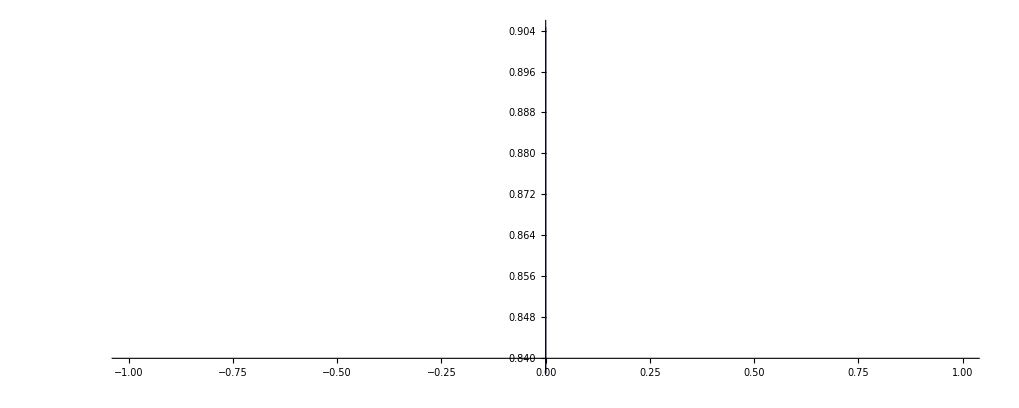

```mathematica
ParametricPlot[{Im[magic[{p}]],Re[magic[{p}]]},{p,2,1000}]
```

```mathematica
Limit[(1/p+1)^(1/Log[p]), p->Infinity]
```

1

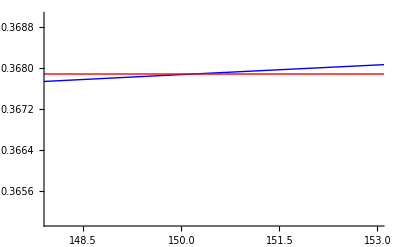

```mathematica
Show[ListPlot[Table[N[magicS[{3,11,13,x}] ], {x,2,200}], Joined->True,PlotStyle->Blue], 
Plot[1/E, {x,2,200}, PlotStyle->Red], PlotRange->{{148,153}, {0.365,0.369}}]
```

```mathematica
Expand[magicS[{p,q}]]
```

2^(-1/Log[p]-1/Log[q]) (1+1/p)^(1/Log[p]) (1+1/q)^(1/Log[q])

```mathematica
Assuming[x >2, SolveAlways[magicS[{3,11,13,x}]==1/E, x]]
```

SolveAlways::dinv: The expression (1 + 1/x)^1/Log[x] involves unknowns in more than one argument, so inverse functions cannot be used.

SolveAlways[(7/13)^(1/Log[13]) 2^(1/Log[3]+1/Log[11]-1/Log[x]) 3^(-1/Log[3]+1/Log[11]) 11^(-1/Log[11]) (1+1/x)^(1/Log[x])==1/ⅇ,x]

```mathematica
N[magicS[{3,11,13,151}]]
```

0.367868